```mathematica
Get["/media/storage/ciencia/trabajo-con-carlos/proyecto-ss/adanerick/codigo/CoolTools.m"]
```

Precision::precsm: Requested precision -5. is smaller than $MinPrecision. Using $MinPrecision instead.

```mathematica
(*Generación de estados de 1 qubit con complejos gaussianos:*)
gaussianStates = randomKets[2,7000];
gaussianStatesBV = densityMatrixToPoint[ketsToDensity[gaussianStates],gellMannBasis[1]];
```

```mathematica
(*Esfera de Bloch con estados gaussianos*)
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[gaussianStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*Ahora estados de 1 qubit generados con la distribución uniforme*)
randomKetsUnif[dim_,m_,min_,max_] := Table[Normalize[Complex @@@ RandomReal[UniformDistribution[{min,max}],{dim,2}]],m]
```

```mathematica
uniformStates = randomKetsUnif[2,7000,-1.3,1.3];
uniformStatesBV = densityMatrixToPoint[ketsToDensity[uniformStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[uniformStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

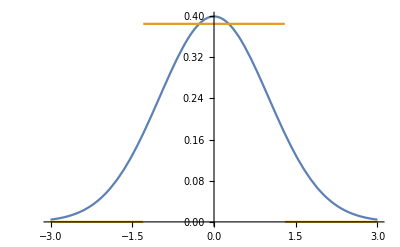

```mathematica
Plot[{PDF[NormalDistribution[],x],PDF[UniformDistribution[{-1.3,1.3}],x]},{x,-3,3}]
```

```mathematica
(*Estados de 1 qubit generados con la distribución Cauchy(0,1) *)
randomKetsCauchy[dim_,m_,a_,b_] := Table[Normalize[Complex @@@ RandomReal[CauchyDistribution[a,b],{dim,2}]],m]
```

```mathematica
cauchyStates = randomKetsCauchy[2,7000,2,1];
cauchyStatesBV = densityMatrixToPoint[ketsToDensity[cauchyStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[cauchyStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*Con la distribución T de Student*)
randomKetsStudentT[dim_,m_,n_] := Table[Normalize[Complex @@@ RandomReal[StudentTDistribution[n],{dim,2}]],m];
```

```mathematica
studentTStates = randomKetsStudentT[2,7000,4];
studentTStatesBV = densityMatrixToPoint[ketsToDensity[studentTStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[studentTStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

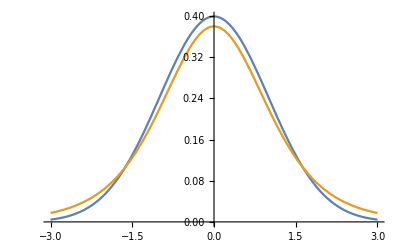

```mathematica
Plot[{PDF[NormalDistribution[],x],PDF[StudentTDistribution[5],x]},{x,-3,3}]
```

Las distribuciones anteriores aceptan valores negativos en sus funciones de densidad, por lo que pueden centrarse en 0 y asemejarse a la ubicación de la distribución normal estándar que usamos originalmente. Veamos, por no dejar, algunas otras distribuciones que sólo aceptan valores positivos.

```mathematica
(*Distribución Beta*)
randomKetsBeta[dim_,m_,α_,β_] := Table[Normalize[Complex @@@ RandomReal[BetaDistribution[α,β],{dim,2}]],m];
```

```mathematica
betaStates = randomKetsBeta[2,7000,2,1/4];
betaStatesBV = densityMatrixToPoint[ketsToDensity[betaStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[betaStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*Distribución Exponencial*)
randomKetsExp[dim_,m_,λ_] := Table[Normalize[Complex @@@ RandomReal[ExponentialDistribution[λ],{dim,2}]],m];
```

```mathematica
expStates = randomKetsExp[2,7000,1];
expStatesBV = densityMatrixToPoint[ketsToDensity[expStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[expStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*distribución Gamma*)
randomKetsGamma[dim_,m_,α_,β_] := Table[Normalize[Complex @@@ RandomReal[GammaDistribution[α,β],{dim,2}]],m];
```

```mathematica
gammaStates = randomKetsGamma[2,7000,1,2];
gammaStatesBV = densityMatrixToPoint[ketsToDensity[gammaStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[gammaStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*Distribución Chi cuadrada*)
randomKetsChiS[dim_,m_,n_] := Table[Normalize[Complex @@@ RandomReal[ChiSquareDistribution[n],{dim,2}]],m];
```

```mathematica
chiSStates = randomKetsChiS[2,7000,0.5];
chiSStatesBV = densityMatrixToPoint[ketsToDensity[chiSStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[chiSStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*Distribución log normal*) 
randomKetsLogN[dim_,m_,μ_,σ_] := Table[Normalize[Complex @@@ RandomReal[LogNormalDistribution[μ,σ],{dim,2}]],m];
```

```mathematica
lognormalStates = randomKetsLogN[2,7000,-1,2];
lognormalStatesBV = densityMatrixToPoint[ketsToDensity[lognormalStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[lognormalStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

```mathematica
(*distibución Weibull (con parámetro de ubicación μ)*)
randomKetsWeibull[dim_,m_,α_,β_,μ_] := Table[Normalize[Complex @@@ RandomReal[WeibullDistribution[α,β,μ],{dim,2}]],m];
```

```mathematica
weibullStates = randomKetsWeibull[2,7000,3,3,-2.5];
weibullStatesBV = densityMatrixToPoint[ketsToDensity[weibullStates],gellMannBasis[1]];
```

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ListPointPlot3D[weibullStatesBV,PlotStyle->PointSize[0.007]]]
```

-Graphics3D-

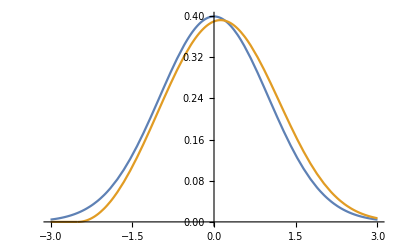

```mathematica
Plot[{PDF[NormalDistribution[],x],PDF[WeibullDistribution[3,3,-2.5],x]},{x,-3,3}]
```